```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(** Data import **)
NamData0=Import["Pure_data/Rhos.txt","Table"];
proj=Import["ideal_proj.txt","Table"];
```

```mathematica
Rho[i_]:={{NamData0[[4+16i,1]],NamData0[[5+16i,1]]},{NamData0[[6+16i,1]],NamData0[[7+16i,1]]}}+{{NamData0[[9+16i,1]],NamData0[[10+16i,1]]},{NamData0[[11+16i,1]],NamData0[[12+16i,1]]}}*I
RhoList1=ParallelTable[Rho[i],{i,0,NamData0[[1,1]]-1}];
```

```mathematica
RhoList1[[124]]//MatrixForm
```

(0.575889+3.8948×10^-18 ⅈ | -0.49419621742625829963202477302+0.0029782801228353306989549143 ⅈ
-0.49419621742625841065432723553-0.00297828012283533199999752128 ⅈ | 0.424111-3.8948×10^-18 ⅈ)

```mathematica
(* HVDARL states *)
StateH={{1},{0}};
StateV={{0},{1}};
StateD=(1/(2^(1/2))){{1},{1}};
StateA=(1/(2^(1/2))){{1},{-1}};
StateR=(1/(2^(1/2))){{1},{I}};
StateL=(1/(2^(1/2))){{1},{-I}};
States = {StateH, StateV, StateD, StateA, StateR, StateL};
Dimensions[States]
```

{6,2,1}

```mathematica
StateToRho[i_]:=States[[i]].ConjugateTranspose[States[[i]]]
Rhos=ParallelTable[StateToRho[i],{i,1,Dimensions[States][[1]]}];
Dimensions[Rhos]
```

{6,2,2}

```mathematica
(* Target sates *)Rho[i_]:={{proj[[4+11i,1]],proj[[5+11i,1]]},{proj[[6+11i,1]],proj[[7+11i,1]]}}+{{proj[[9+11i,1]],proj[[10+11i,1]]},{proj[[11+11i,1]],proj[[12+11i,1]]}}*I
RhoListProj=ParallelTable[Rho[i],{i,0,proj[[1,1]]-1}];
Dimensions[RhoListProj]
```

{120,2,2}

```mathematica
RhoTarget=RhoListProj;
```

```mathematica
sigma2={{0,1},{1,0}};
sigma3={{0,-I},{I,0}};
sigma1={{1,0},{0,-1}};
sigma={sigma1,sigma2,sigma3};(* Sigma matrices *) 
stokesStates[i_,x_]:=ConjugateTranspose[States[[x]]].sigma[[i]].States[[x]]
stokeslistStates=ParallelTable[ Re[stokesStates[i,x][[1,1]]],{x,1,Dimensions[States][[1]]},{i,1,3}  ];
```

```mathematica
Fidelity[Rho1_,Rho2_,i_,j_]:=Re[Tr[MatrixPower[MatrixPower[Rho1[[i]],1/2].Rho2[[j]].MatrixPower[Rho1[[i]],1/2],1/2]]]^2
```

```mathematica
(** 120 states **)FidelityList1=ParallelTable[Fidelity[RhoTarget,RhoList1,i,j],{j,1,Dimensions[RhoList1][[1]]},{i,1,Dimensions[RhoTarget][[1]]}];FidelityListTrans1=Transpose[FidelityList1];PosTable1=ParallelTable[Position[FidelityListTrans1,Max[FidelityListTrans1[[i]]]],{i,1,Dimensions[FidelityListTrans1][[1]]}];BestFidelitys1=ParallelTable[FidelityList1[[PosTable1[[i,1,2]],PosTable1[[i,1,1]]]],{i,1,Dimensions[PosTable1][[1]]}];
```

```mathematica
BestRhoList1=ParallelTable[RhoList1[[PosTable1[[i,1,2]]]],{i,1,Dimensions[PosTable1][[1]]}];
```

```mathematica
RhoToStokes[Rho_,i_,j_]:=Re[Tr[Rho[[i]].sigma[[j]]]]
```

```mathematica
StokesList1=ParallelTable[RhoToStokes[RhoList1,i,j],{i,1,Dimensions[RhoList1][[1]]},{j,1,Dimensions[sigma][[1]]}];
stokeslistStates=ParallelTable[RhoToStokes[Rhos,i,j],{i,1,Dimensions[Rhos][[1]]},{j,1,Dimensions[sigma][[1]]}];
BestStates1=ParallelTable[RhoToStokes[BestRhoList1,i,j],{i,1,Dimensions[BestRhoList1][[1]]},{j,1,Dimensions[sigma][[1]]}];
```

```mathematica
StokesListTarget=ParallelTable[RhoToStokes[RhoTarget,i,j],{i,1,Dimensions[RhoTarget][[1]]},{j,1,Dimensions[sigma][[1]]}];
```

```mathematica
(** Fidelity **)
```

```mathematica
BestFidelitys1;
Max[BestFidelitys1]
Min[BestFidelitys1]
StandardDeviation[BestFidelitys1]
```

0.999997

0.994605

0.00114606

```mathematica
Sum[BestFidelitys1[[i]],{i,1,120}]/Dimensions[BestFidelitys1][[1]]
```

0.99942

```mathematica
0.9994204546069704s
```

0.99942 s

```mathematica
(** Purity  **)
Purity[Rho_]:=Re[Tr[MatrixPower[Rho,2]]]
```

```mathematica
BestPuritys1=ParallelTable[Purity[BestRhoList1[[i]]],{i,1,Dimensions[BestRhoList1][[1]]}];
Max[BestPuritys1]
Min[BestPuritys1]
StandardDeviation[BestPuritys1]
```

0.999999

0.989427

0.00226655

```mathematica
Sum[BestPuritys1[[i]],{i,1,Dimensions[BestPuritys1][[1]]}]/Dimensions[BestPuritys1][[1]]
```

0.999063

```mathematica
(** Angles **)
```

```mathematica
AngleVec[u_,v_]:=ArcCos[(u[[1]]*v[[1]]+u[[2]]*v[[2]]+u[[3]]*v[[3]])/(Sqrt[u[[1]]^2+u[[2]]^2+u[[3]]^2]*Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2])]
Angles1=Table[AngleVec[BestStates1[[i]],StokesListTarget[[i]]],{i,1,120}];
```

```mathematica
StandardDeviation[Angles1];
```

```mathematica
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"];
```

```mathematica
%/2
```

0.270545 °

```mathematica
Sum[Angles1[[i]],{i,1,Dimensions[Angles1][[1]]}]/Dimensions[Angles1][[1]];
```

```mathematica
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"];
```

```mathematica
%/2
```

0.535725 °

```mathematica
(** Hammer projestion **)
GetSpherical[Stokes_]:={ArcTan[Sqrt[Stokes[[2]]^2+Stokes[[1]]^2],Stokes[[3]]],Limit[ArcTan[x,Stokes[[2]]],{x->Stokes[[1]]}]}
```

```mathematica
HammerCoordinates[stokes_]:=ArrayReshape[{(2*Sqrt[2] * Cos[elev]*Sin[az/2])/Sqrt[1+Cos[elev] Cos[az/2]],(Sqrt[2] * Sin[elev])/Sqrt[1+Cos[elev] Cos[az/2]]}/.{elev->GetSpherical[stokes][[1]],az->GetSpherical[stokes][[2]]},{2}]
```

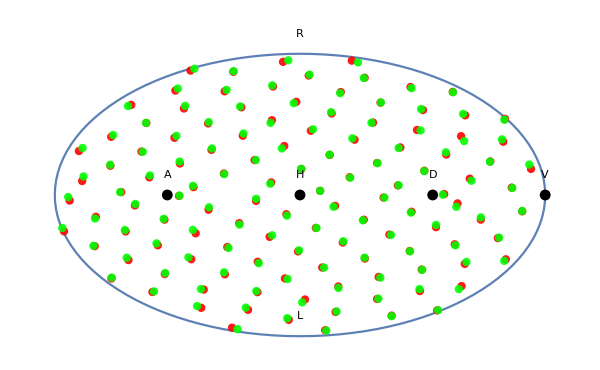

```mathematica
Show[ListPlot[Table[ArrayReshape[{(2*Sqrt[2] * Cos[elev]*Sin[az/2])/Sqrt[1+Cos[elev] Cos[az/2]],(Sqrt[2] * Sin[elev])/Sqrt[1+Cos[elev] Cos[az/2]]}/.{elev->Range[0.,2*Pi,2*Pi/120][[i]],az->Pi},{2}],{i,1,121}],Joined->{True,False}],
ListPlot[Table[HammerCoordinates[StokesListTarget[[i]]],{i,1,120}],PlotStyle->{PointSize[0.01],RGBColor[1,0,0],Opacity[0.9]}],ListPlot[Table[HammerCoordinates[BestStates1[[i]]],{i,1,120}],PlotStyle->{PointSize[0.01],RGBColor[0,1,0],Opacity[0.9]}],ListPlot[Table[HammerCoordinates[stokeslistStates[[i]]],{i,1,6}],PlotStyle->{PointSize[0.013],RGBColor[0,0,0]}],
Graphics[Style[Text["H",{0,0.2}],Black,Italic,30]],
Graphics[Style[Text["V",{2 √2,0.2}],Black,Italic,30]],
Graphics[Style[Text["D",{2/(√(1+1/(√2))),0.2}],Black,Italic,30]],
Graphics[Style[Text["A",{-2/(√(1+1/(√2))),0.2}],Black,Italic,30]],
Graphics[Style[Text["R",{0,√2+0.2}],Black,Italic,30]],
Graphics[Style[Text["L",{0,-√2+0.2}],Black,Italic,30]],
PlotRange->All,Axes->False,ImageSize->600]
```